## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="ENO";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_ENO_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 6.69595 | 6.36116
7.03075 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 626.718 | 595.382
658.054 | 1/s | 8.1 | 37 | trishcl | 0.05 | cl | 0.1
k | 0.1
1 | pep | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 6.69595 | 6.36116
7.03075 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 626.718 | 595.382
658.054 | 1/s | 8.1 | 37 | trishcl | 0.05 | cl | 0.1
k | 0.1
1 | pep | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_ENO[c] + 2pg[c] <=> E_ENO[c]&2pg",
				"E_ENO[c]&2pg <=> E_ENO[c]&pep",
				"E_ENO[c]&pep <=> E_ENO[c] + pep[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,Overscript[(ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c, ENO2],((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((ENO^c&(2pg)^c)_^-((ENO^c&pep^c)_^)/K_ENO3) Volume_c k_ENO3^⟶}

Volume_c (-(ENO^c&pep^c)_^ k_ENO3^⟵+(ENO^c&(2pg)^c)_^ k_ENO3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.0012546434607581675;
FluxExpression = absoluteFlux /. {metabolite["2pg", "c"] -> 0.0001235162508685228,metabolite["pep","c"]-> 0,
     parameter["ENO_total"] -> 0.0000857539368988014, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "ENO"] /. FluxExpression;
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt"	6.69595445
1	0.00001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt"	0.9090909090909091
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	1	0	1	8.1	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675

### Simulate data with uncertainty

```mathematica
Null
```

```mathematica
Null
```

### Parameter scan

```mathematica
Null
```

```mathematica
Null
```

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 10.1832039589
best_fit: 10.183204124
best_fit: 10.1832091981
best_fit: 10.1832039398
best_fit: 10.1832042241
best_fit: 10.18320394
best_fit: 10.1832039568
best_fit: 10.1832039477
best_fit: 10.183205119
best_fit: 10.1832042076

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_typeII/input/FBA2.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | haldaneRatio_1 | 0.0000553646 | 3.06524×10^-9 | 0.000853558 | 0.0127474 | 6.69595 | 6.6951
1 | relRateFor_2pg | 0.912472 | 0.832605 | 0.0797883 | 87.7671 | 0.0909091 | 0.0111208
1 | relRateFor_2pg | 0.892786 | 0.797066 | 0.119295 | 87.1999 | 0.136807 | 0.0175115
1 | relRateFor_2pg | 0.863776 | 0.74611 | 0.173287 | 86.3157 | 0.20076 | 0.0274727
1 | relRateFor_2pg | 0.822476 | 0.676466 | 0.241894 | 84.9504 | 0.284747 | 0.0428533
1 | relRateFor_2pg | 0.766315 | 0.587239 | 0.320605 | 82.8729 | 0.386863 | 0.0662586
1 | relRateFor_2pg | 0.694226 | 0.48195 | 0.398902 | 79.7803 | 0.5 | 0.101098
1 | relRateFor_2pg | 0.607742 | 0.369351 | 0.461845 | 75.325 | 0.613137 | 0.151292
1 | relRateFor_2pg | 0.511437 | 0.261568 | 0.494949 | 69.1991 | 0.715253 | 0.220304
1 | relRateFor_2pg | 0.412249 | 0.169949 | 0.489905 | 61.2964 | 0.79924 | 0.309335
1 | relRateFor_2pg | 0.317844 | 0.101025 | 0.447986 | 51.8987 | 0.863193 | 0.415207
1 | relRateFor_2pg | 0.234687 | 0.0550778 | 0.379524 | 41.7477 | 0.909091 | 0.529567
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateFor | 0.646254 | 0.417644 | 485.198 | 77.4188 | 626.718 | 141.52
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
1 | absRateRev | 0.0000534915 | 2.86134×10^-9 | 0.0036983 | 0.0123161 | 30.0281 | 30.0244
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028
3 | customRatio_1 | 0.0718242 | 0.00515872 | 0.000225639 | 17.9843 | 0.00125464 | 0.00148028

### Simulated Data and Best Fit Data Plot

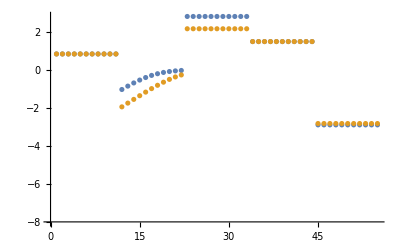

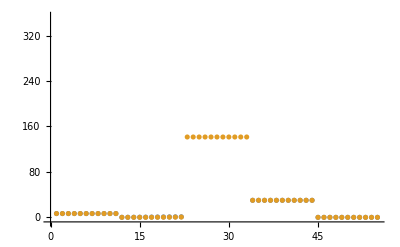

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

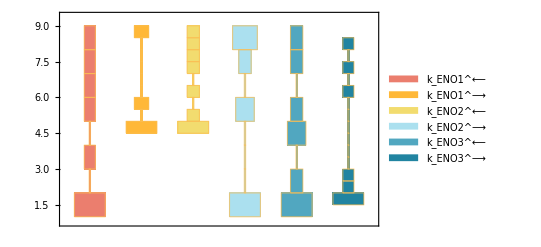

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

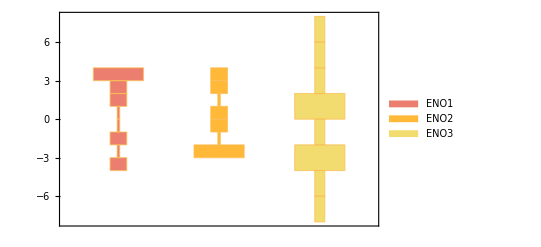

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

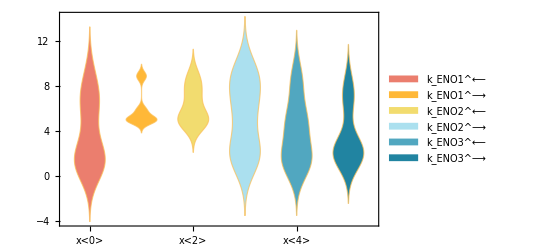

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

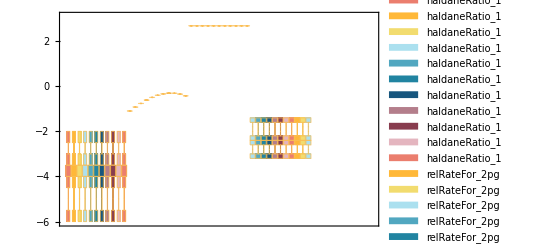

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0001 | 0.000888436 | 788.436

```mathematica
assumedSaturatingConc
```

1

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 141.52 | 77.4188
30.0281 | 30.0244 | 0.0123161

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
6.69595 | 6.6951 | 0.0127474

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
6.69595 | 6.6951 | 0.0127474

```mathematica
MASSef
```

MASSef

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

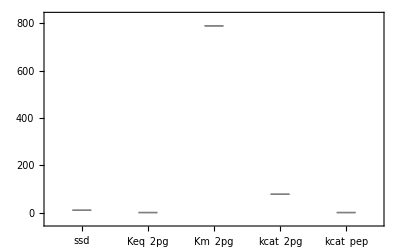

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse]
```

{{absRateFor,absRateRev,relRateFor_2pg,relRateRev_pep},{(2 (2pg)^c ENO_total_Global k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),(2 pep^c ENO_total_Global k_ENO1^⟵ k_ENO2^⟵ k_ENO3^⟵)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶)),((2pg)^c (k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),(pep^c (k_ENO1^⟵ (k_ENO2^⟵+k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO2^⟵ (k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶))},{(2*d[0]*d[2]*x[1]*x[3]*x[5])/(x[0]*(x[3] + x[4]) + x[3]*x[5] + d[0]*x[1]*(x[3] + x[4] + x[5])),(2*d[1]*d[2]*x[0]*x[2]*x[4])/(x[0]*(x[3] + x[4]) + x[3]*x[5] + d[1]*x[2]*(x[0] + x[4] + x[5])),(d[0]*(x[0]*(x[3] + x[4]) + x[3]*x[5] + x[1]*(x[3] + x[4] + x[5])))/(x[0]*(x[3] + x[4]) + x[3]*x[5] + d[0]*x[1]*(x[3] + x[4] + x[5])),(d[1]*(x[0]*(x[2] + x[3] + x[4]) + x[3]*x[5] + x[2]*(x[4] + x[5])))/(x[0]*(x[3] + x[4]) + x[3]*x[5] + d[1]*x[2]*(x[0] + x[4] + x[5]))},{/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateRev_pep.txt},{/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateFor.txt→(2 (2pg)^c ENO_total_Global k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/absRateRev.txt→(2 pep^c ENO_total_Global k_ENO1^⟵ k_ENO2^⟵ k_ENO3^⟵)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶)),/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateFor_2pg.txt→((2pg)^c (k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_MASSpy_typeII/input/relRateRev_pep.txt→(pep^c (k_ENO1^⟵ (k_ENO2^⟵+k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO2^⟵ (k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶))}}

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/eno already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\rateconst_labels_eno.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\S_eno.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_ENO[c],E_ENO[c]&2pg,2pg[c],pep[c],E_ENO[c]&pep}

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\species_eno.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{ENO1: 2pg[c] + E_ENO[c] <=> E_ENO[c]&2pg,ENO2: E_ENO[c]&pep <=> E_ENO[c] + pep[c],ENO3: E_ENO[c]&2pg <=> E_ENO[c]&pep}

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\reactions_eno.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_ENO[c],E_ENO[c]&2pg,E_ENO[c]&pep}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_ENO1_rev*k_ENO2_fwd*param_ENO_total) - k_ENO2_fwd*k_ENO3_fwd*param_ENO_total - k_ENO1_rev*k_ENO3_rev*param_ENO_total)/(2pg(c)*k_ENO1_fwd*k_ENO2_fwd + k_ENO1_rev*k_ENO2_fwd + 2pg(c)*k_ENO1_fwd*k_ENO3_fwd + k_ENO2_fwd*k_ENO3_fwd + 2pg(c)*k_ENO1_fwd*k_ENO3_rev + k_ENO1_rev*k_ENO3_rev + k_ENO1_rev*k_ENO2_rev*pep(c) + k_ENO2_rev*k_ENO3_fwd*pep(c) + k_ENO2_rev*k_ENO3_rev*pep(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\rateconst_clusters_eno.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/eno\rateLaw_eno.txt